```mathematica
ASSIGNMENT - 5
```

Om Gupta
214047

```mathematica
Q1.x’(t)+y’(t)-x(t)=2t
x’(t)+y’(t)-3x(t)-y(t)=t^2
```

Syntax::sntxb: Expression cannot begin with "Q1.x’(t)+y’(t)-x(t)=2t
x’(t)+y’(t)".

```mathematica
eqn1a=x'[t]+y'[t]-x[t]==2 t
eqn1b=x'[t]+y'[t]-3 x[t]-y[t]==t^2
sol1=DSolve[{eqn1a,eqn1b},{x[t],y[t]},t]
```

-x[t]+x'[t]+y'[t]==2 t

-3 x[t]-y[t]+x'[t]+y'[t]==t^2

{{x[t]→2 t-t^2+1/4 (4 (6-6 t+t^2)-ⅇ^-t C[1]),y[t]→-2 t+t^2+1/2 (-4 (6-6 t+t^2)+ⅇ^-t C[1])}}

```mathematica
sol11={x[t],y[t]}/. sol1/. C[1]->2
```

{{2 t-t^2+1/4 (-2 ⅇ^-t+4 (6-6 t+t^2)),-2 t+t^2+1/2 (2 ⅇ^-t-4 (6-6 t+t^2))}}

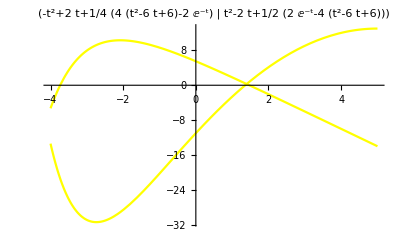

```mathematica
Plot[sol11,{t,-4,5},PlotStyle->Yellow, PlotLabel->sol11]
```

```mathematica
Q2.x’(t)+y(t)=0
y’(t)+x(t)=0
```

```mathematica
eqn2a=x'[t]+y[t]==0
eqn2b=y'[t]+x[t]==0
sol2=DSolve[{eqn2a,eqn2b},{x[t],y[t]},t]
```

y[t]+x'[t]==0

x[t]+y'[t]==0

{{x[t]→1/2 ⅇ^-t (1+ⅇ^(2 t)) C[1]-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[2],y[t]→-1/2 ⅇ^-t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^-t (1+ⅇ^(2 t)) C[2]}}

```mathematica
sol21={x[t],y[t]}/. sol2/. {C[1]->2,C[2]->2}
```

{{-ⅇ^-t (-1+ⅇ^(2 t))+ⅇ^-t (1+ⅇ^(2 t)),-ⅇ^-t (-1+ⅇ^(2 t))+ⅇ^-t (1+ⅇ^(2 t))}}

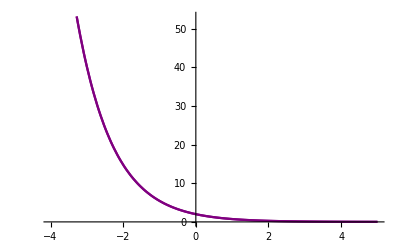

```mathematica
Plot[sol21,{t,-4,5},PlotStyle->Purple]
```